# Project Euler Problem 14

This would have required more thought back in 2002, but with a reasonable memory size this can be handled quite nicely with memoization:

```mathematica
collatzLength[1]=0;
collatzLength[n_]:=collatzLength[n]=If[EvenQ[n],1+collatzLength[n/2],2+collatzLength[(3n+1)/2]]
```

```mathematica
collatzSequence[n_]:=NestWhileList[If[EvenQ[#],#/2,3#+1]&,n,#>1&]
```

```mathematica
collatzLength/@Range[1000000];
```

```mathematica
MemoryInUse[]
```

353832696

```mathematica
Length[DownValues[collatzLength]]
```

1588208

```mathematica
{pmax,max}=With[{vals=collatzLength/@Range[1000000]},{max=Max[vals]},{First[FirstPosition[vals,max]],max}]
```

{837799,524}

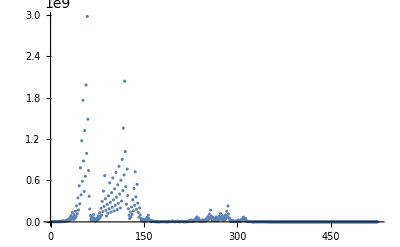

```mathematica
ListPlot[collatzSequence[pmax],PlotRange->All]
```